```mathematica
n = 3;
Clear[taylor]
fun[x_]=Sin[x] x^2 Exp[-x];
taylor[x_] = Normal[Series[fun[x],{x,2,n}]];
```

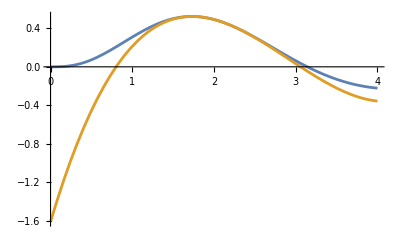

```mathematica
Plot[{fun[x],taylor[x]},{x,0,4}]
```

```mathematica
Manipulate[Plot[{fun[x],Evaluate[Normal[Series[fun[x],{x,2,Round[n]}]]]},{x,0,4}],{n,1,10}]
```